```mathematica
Clear["Global`*"]
data=Import["~/Desktop/sun.jpg","Data"];
data=Drop[data,1];
image=Table[
Mean[Mean[
data⟦11i+1;;11(i+1),11j+1;;11(j+1)⟧
]],
{i,0,(Length[data])/11-1},
{j,0,(Length[data⟦1⟧])/11-1}]/255.;
```

```mathematica
Image[image,ColorSpace->"RGB"]
```

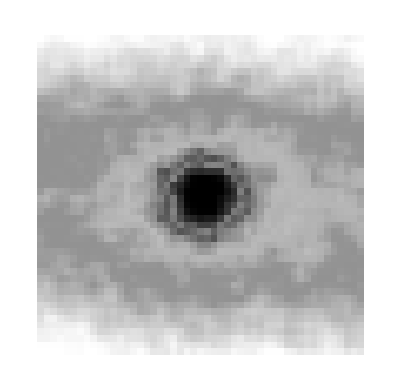

```mathematica
image2=Map[Mean,image,{-2}];
```

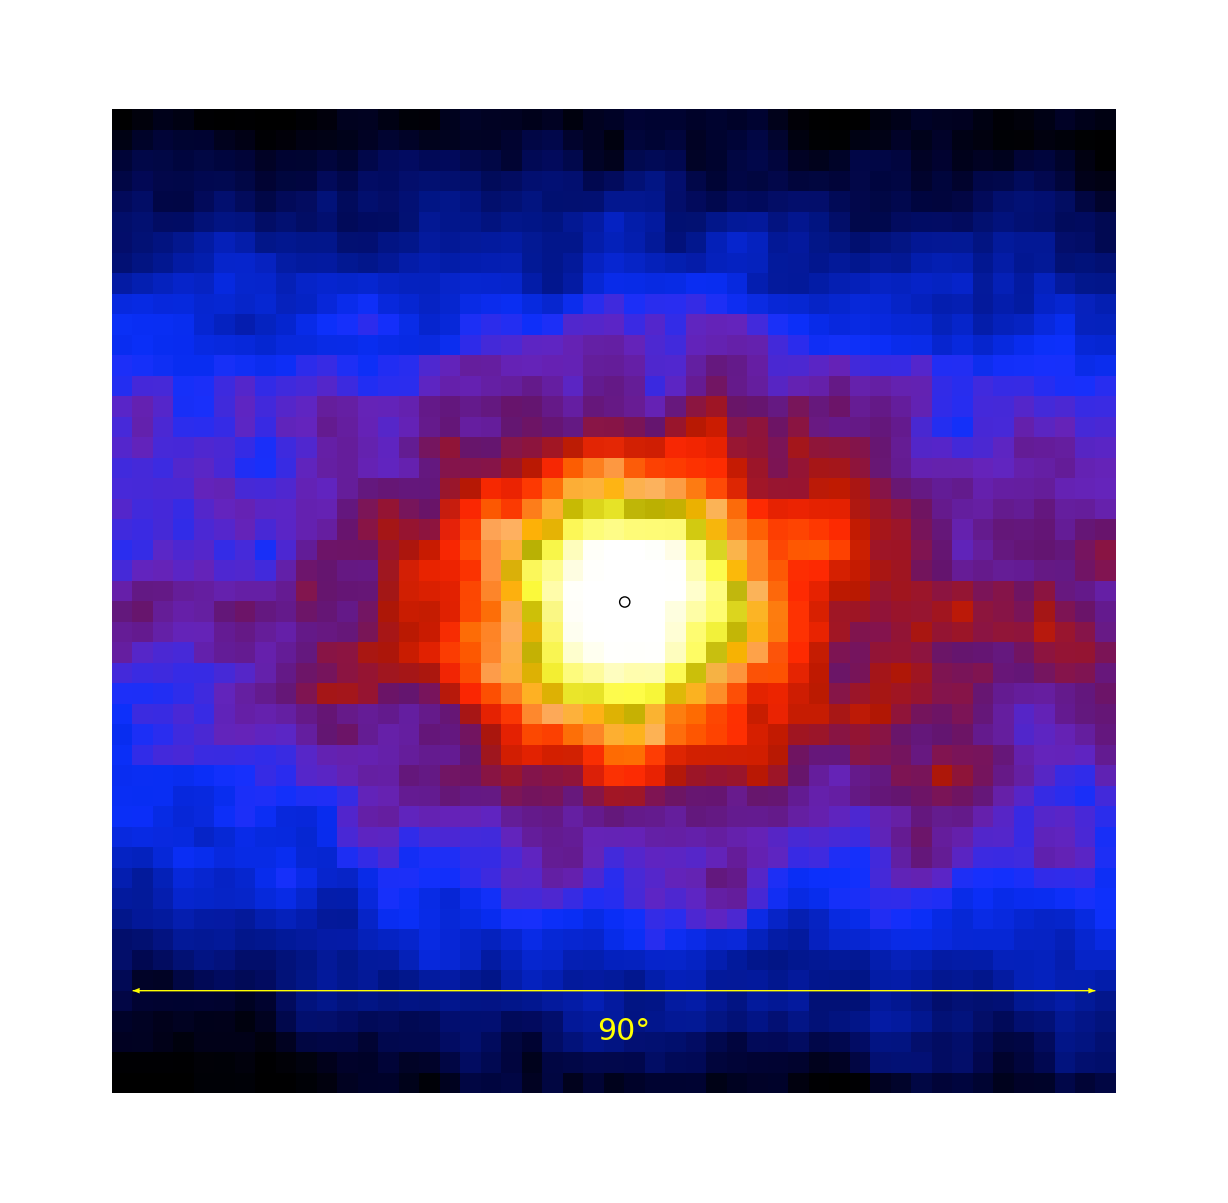

```mathematica
Show[
Image[image,ColorSpace->"RGB"],
Graphics[{
Thick,
Circle[{25,24},0.25],
Arrowheads[{-.02,.02}],Yellow,
Arrow[{{1,5},{48,5}}],
Text[Style["90°",FontFamily->"Times",FontSize->30],{25,3}]
}]
]
```

```mathematica
image//Length
```

48

```mathematica
image[[20]]/255.
```

{{0.329703,0.150251,0.796435},{0.256522,0.163734,0.861157},{0.269324,0.15858,0.850527},{0.21076,0.169146,0.897683},{0.328051,0.150057,0.796046},{0.388073,0.141047,0.74364},{0.394879,0.133528,0.705655},{0.356539,0.145163,0.770021},{0.355015,0.144677,0.775109},{0.391898,0.130676,0.689159},{0.397213,0.133528,0.700891},{0.392027,0.0918166,0.492368},{0.487376,0.0807649,0.339362},{0.582272,0.0789823,0.201232},{0.465143,0.0811862,0.357284},{0.411441,0.0775887,0.409107},{0.780068,0.114925,0.0529898},{0.979517,0.151677,0.00742181},{0.989208,0.343672,0.00826446},{0.986193,0.228683,0.00664398},{0.993291,0.490002,0.101766},{0.993032,0.680441,0.187652},{0.780036,0.728504,0.0171771},{0.861676,0.836947,0.105007},{0.902317,0.889386,0.15427},{0.748242,0.711846,0.0264139},{0.732782,0.691557,0.00923675},{0.773165,0.691946,0.00949603},{0.922573,0.695252,0.00476422},{0.982726,0.701928,0.337352},{0.988527,0.419057,0.0407389},{0.991671,0.166164,0.00722735},{0.902382,0.133657,0.00683844},{0.923416,0.136477,0.00635229},{0.896678,0.133398,0.00463458},{0.89415,0.129801,0.00408362},{0.68621,0.0926916,0.0655647},{0.609626,0.0811862,0.158905},{0.54001,0.0783666,0.26093},{0.435975,0.0797278,0.379776},{0.395722,0.103322,0.551969},{0.393129,0.116902,0.62139},{0.39825,0.121795,0.64048},{0.391217,0.10666,0.558289},{0.394004,0.108313,0.582953},{0.392384,0.0905526,0.496419},{0.394588,0.116027,0.61883},{0.39744,0.113758,0.606838},{0.398153,0.128115,0.673343}}